## Bayesian Statistics, Assignment for Tuesday, Nov. 19

## Reading

You can proceed through Chapter 11, which introduces gamma functions which are conjugate to Poisson distributions. The development in Chapter 11 is exactly analogous to Chapter 10 where you saw that beta functions are conjugate to binomial distributions. Alternatively, you can just study my handout on Bayesian conjugates. It is up to you, as long as you understand the take-home points from Chapters 10 and 11.

## For Problem Set 14

### 1. The Field Goal Problem

Let’s assume that kickers from the NFL can make field goals from 70-yard line with 27% success rate in 2020, using the latest data we have (see graph). Of course, some kickers will have a higher success rate at that distance and some lower.

-Graphics-

(a) Knowing that the mean, μ, of a beta distribution is given by Donovan and Mickey as μ=α/(α+β), and accepting that β=8 (quite frankly, I chose that value of β for no good reason other than to make some other things come somewhat tidily), what integer choice for α gives you a μ that is close to 27%?

(b) Knowing that the variance, σ^2, of a beta distribution is given by Donovan and Mickey as σ^2=αβ/((α+β)^2(α+β+1)), and using the value for α you chose in (a), what is σ^2? Also what is the standard deviation, σ?

(c) Make a strong vertical line on the plot below at p=0.27. Notice this plot has “skew” (a fancy word for saying that one tail of the distribution is more substantial than the other). So your vertical line will not go right through the peak of the curve.

(c) Also make vertical lines at μ-σ and μ+σ and then shade everything in between.

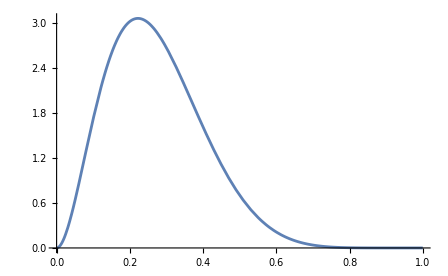

```mathematica
nonNormalizedBeta[p_,α_, β_]:=p^(α-1)(1-p)^(β-1);
normalization[α_, β_]:=Integrate[nonNormalizedBeta[q, α, β], {q, 0, 1}];
normalizedBeta[p_, α_, β_]:=nonNormalizedBeta[p,α,β]/normalization[α,β];
Plot[normalizedBeta[p, 3, 8], {p, 0, 1}]
```

(d) Estimate (you can be crude in your estimate) the area of the shaded region and convert this to a percentage. If this were a Gaussian distribution (it looks a little like one, but it is definitely a beta distribution, not a Gaussian), then 68% of the area of the curve would be shaded. The 68% rule only applies to Gaussians, but it is often pretty good for other curves that look like Gaussians.



(e) Interpret what you found as a couple of sentences that you could put in a paper by filling in the blanks:

Admittedly somewhat arbitrarily, we modeled the 2020 field goal success rate at 70 yards for all kickers in the NFL with a beta function with α=3 and β=8. This beta function has mean ________. With this beta function we expect ____________ of the kickers to have success rates between _______ and ______.

### 2. The Great Kicker

I don’t know squat about football, so the stats below are even more contrived than in Problem 1.

Stephen Gostkowski opens his 2021 season with two games in which he attempts kicks from the 70-yard line. Your prior for his success rate is the prior you found in Problem 1. You’d predict 0.27 for his success rate.

In fact, he makes one kick and he misses one kick. Not knowing Bayesian statistics, you might now say that he makes 70-yard kicks with p=0.5.

But you know Bayesian statistics, so instead you compute the likelihood for 2 attempts with 1 success and take the product of that with the prior that  you investigated in Problem 1 to get a posterior. This is a bit of work, but you can readily do it! A bit of scratch space:



(a) What are the α and β in the posterior? When you write your answer for the new α and β, let’s call these α_1 and β_1 since we have already used α=3 and β=8 for the prior you analyzed in Problem 1, and it will get mighty confusing if we use exactly the same variable names for the parameters in the posterior.


(b) What is the new mean, μ_1?


(c) What is the new variance, σ_1^2, and the new standard deviation, σ_1?


(d) Don’t do this, but can you see how this posterior becomes your new prior if you get, say, three more games of data in which Gostkowski is 1 for 3 of 70-yard kicks?

And can you see that you would get yet another posterior by incorporating the likelihood for 3 attempts with 1 success with the parameters you wrote down in 2(a)? You could call these new posterior parameters α_2 and β_2.

If you were a football stats junkie, perhaps you would have a computer program that calculates a new posterior every time a new game result comes, and then uses that as the prior when the result after that comes in.